# Audio

```mathematica
a=Audio["E:\\KuGou\\kanon - 雪之少女.mp3"]
```

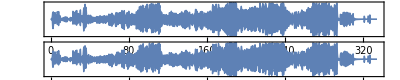

```mathematica
AudioPlot[a]
```

```mathematica
AudioData[a]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,14754742,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},1}
 |  |  |  |

```mathematica
hfc=Rescale@AudioLocalMeasurements[a,"HighFrequencyContent"];
```

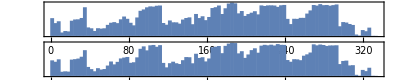

```mathematica
Quiet@AudioPlot[a,PlotRange->{All,All},Appearance->"DiscreteAbs",ColorFunction->Function[{x,y},ColorData["SunsetColors"]@hfc[x]]]
```